# Homework 4 Homework Assignment 4: A seesaw catalyst - Data analysis

## CRN Simulator

Chemical Reaction Network (CRN) Simulator package is developed by David Soloveichik. Copyright 2009-2015. 
http://users.ece.utexas.edu/~soloveichik/crnsimulator.html

### Public interface specification

```mathematica
Notation`AutoLoadNotationPalette = False;
Needs["Notation`"]
BeginPackage["CRNSimulator`", {"Notation`"}];
```

```mathematica
rxn::usage="Represents an irreversible reaction. eg. rxn[a+b,c,1]";
revrxn::usage="Represents a reversible reaction. eg. revrxn[a+b,c,1,1]";
conc::usage="Initial concentration: conc[x,10] or conc[{x,y},10].";
term::usage="Represents an additive term in the ODE for species x. \
Species concentrations must be expressed in x[t] form. eg. term[x, -2 x[t]*y[t]]";
```

```mathematica
SimulateRxnsys::usage=
"SimulateRxnsys[rxnsys,endtime] simulates the reaction system rxnsys for time 0 \
to endtime. In rxnsys, initial concentrations are specified by conc statements. \
If no initial condition is set for a species, its initial concentration is set to 0. \
Rxnsys can also include term[] statements (e.g. term[x, -2 x[t]]) which are additively \
combined together with term[]s derived from rxn[] statements. \
Rxnsys can also include direct ODE definitions for some species (e.g. x'[t]==...), \
or direct definitions of species as functions of time (e.g. x[t]==...), \
which are passed to NDSolve without modification. \
Any options specified (eg WorkingPrecision->30) \
are passed to NDSolve."; 
SpeciesInRxnsys::usage=
"SpeciesInRxnsys[rxnsys] returns the species in reaction system rxnsys. \
SpeciesInRxnsys[rxnsys,pttrn] returns the species in reaction system rxnsys \
matching Mathematica pattern pttrn (eg x[1,_]).";
SpeciesInRxnsysStringPattern::usage=
"SpeciesInRxnsysPattern[rxnsys,pttrn] returns the species in reaction system rxnsys \
matching Mathematica string pattern pttrn. \
(Eg \"g$*\" matches all species names starting with \"g$\" ; \ 
can also do RegularExpression[\"o..d.\$.*\"].)";
RxnsysToOdesys::usage=
"RxnsysToOdesys[rxnsys,t] returns the ODEs corresponding to reaction system rxnsys, \
with initial conditions. If no initial condition is set for a species, its initial \
concentration is set to 0. \
The time variable is given as the second argument; if omitted it is set to Global`t.";
```

```mathematica
(*To use instead of Sequence in functions with Hold attribute but not HoldSequence,
like Module, If, etc*)
Seq:=Sequence
```

### Private

```mathematica
Begin["`Private`"];
```

```mathematica
Notation[ParsedBoxWrapper[RowBox[{"r_", " ", OverscriptBox["→", RowBox[{" ", "k_", " "}]], " ", "p_", " "}]] ⟺ ParsedBoxWrapper[RowBox[{"rxn", "[", RowBox[{"r_", ",", "p_", ",", "k_"}], "]"}]]]
Notation[ParsedBoxWrapper[RowBox[{"r_", " ", UnderoverscriptBox["⇄", "k2_", "k1_"], " ", "p_", " "}]] ⟺ ParsedBoxWrapper[RowBox[{"revrxn", "[", RowBox[{"r_", ",", "p_", ",", "k1_", ",", "k2_"}], "]"}]]]
AddInputAlias[ParsedBoxWrapper[RowBox[{"□", " ", OverscriptBox["→", RowBox[{" ", "□", " "}]], " ", "□", " "}]],"rxn"]
AddInputAlias[ParsedBoxWrapper[RowBox[{"□", " ", UnderoverscriptBox["⇄", "□", "□"], " ", "□", " "}]],"revrxn"]
```

```mathematica
(*We want rxn[a+b,c,1] to be different from rxn[b+a,c,1], so we have to set attribute
HoldAll. But we also want to evaluate if any variables can be evaluated.*)
SetAttributes[{rxn,revrxn}, HoldAll]
rxn[rs_Plus,ps_,k_]:=
 ReleaseHold[ReplacePart[rxn[1,ps,k],1->Hold[Plus]@@List@@Unevaluated[rs]]]/;
 Hold@@Unevaluated[rs] =!= Hold@@List@@Unevaluated[rs]
rxn[rs_,ps_Plus,k_]:=
 ReleaseHold[ReplacePart[rxn[rs,1,k],2->Hold[Plus]@@List@@Unevaluated[ps]]]/;
 Hold@@Unevaluated[ps] =!= Hold@@List@@Unevaluated[ps]
rxn[rs_,ps_,k_]:=
 (With[{rse=rs},rxn[rse,ps,k]])/;Head[rs]=!=Plus&&Unevaluated[rs]=!=rs
rxn[rs_,ps_,k_]:=
 (With[{pse=ps},rxn[rs,pse,k]])/;Head[ps]=!=Plus&&Unevaluated[ps]=!=ps
rxn[rs_,ps_,k_]:=
 (With[{ke=k},rxn[rs,ps,ke]])/;Unevaluated[k]=!=k
```

```mathematica
(* Automatically expand revrxn and concentration lists *)
revrxn[r_,p_,k1_,k2_]:=Sequence[rxn[r,p,k1],rxn[p,r,k2]]
conc[xs_List,c_]:=Seq@@(conc[#,c]&/@xs)

(* People are often confused about rxn[0,x,1] instead of rxn[1,x,1]. So we automatically replace any integer with 1. *)
rxn[Except[1,_Integer],ps_,k_]:=rxn[1,ps,k]
```

```mathematica
(* Species as products or reactants in rxn[] statements, as well as defined in x'[t]== or x[t]== statements \
or term statements, or conc statements *)
SpeciesInRxnsys[rxnsys_]:=
 Union[
 	Cases[Cases[rxnsys,rxn[r_,p_,_]:>Seq[r,p]]/.Times|Plus->Seq,s_Symbol|s_Symbol[__]],
 	Cases[rxnsys, x_'[_]==_ | x_[_]==_ | term[x_,__] | conc[x_,_] :> x]]
SpeciesInRxnsys[rsys_,pattern_]:=Cases[SpeciesInRxnsys[rsys],pattern]
SpeciesInRxnsysStringPattern[rsys_,pattern_]:=Select[SpeciesInRxnsys[rsys],StringMatchQ[ToString[#],pattern]&]
```

```mathematica
(* Check if a species' initial value is set in a odesys *) 	
InitialValueSetQ[odesys_,x_]:=
 MemberQ[odesys,x[_]==_]

(* Check if a species is missing an ODE or a direct definition (x[t]=_) in odesys. *)
MissingODEQ[odesys_,x_,t_Symbol]:=
 !MemberQ[odesys, D[x[t],t]==_ | x[t]==_]  	

RxnsysToOdesys[rxnsys_,t_Symbol:Global`t]:=
 Module[
  {spcs=SpeciesInRxnsys[rxnsys], concs, termssys, odesys, eqsFromTerms, eqsFromConcs},

  (* extract conc statements and sum them for same species *)
  concs = conc[#[[1,1]],Total[#[[;;,2]]]]&/@GatherBy[Cases[rxnsys,conc[__]],Extract[{1}]];

  (* Convert rxn[] to term[] statements *)
  termssys=rxnsys /. rxn:rxn[__]:>Seq@@ProcessRxnToTerms[rxn,t];

  (* ODEs from parsing terms *)
  eqsFromTerms = ProcessTermsToOdes[Cases[termssys,term[__]],t]; 
  (* initial values from parsing conc statements *)
  eqsFromConcs = Cases[concs,conc[x_,c_]:>x[0]==c]; 

  (* Remove term and conc statements from rxnsys and add eqs generated from them. 
     If there is a conflict, use pass-through equations *)
  odesys = DeleteCases[termssys, term[__]|conc[__]];
  odesys = Join[odesys,
                DeleteCases[eqsFromTerms, Alternatives@@(#'[t]==_& /@ Cases[odesys,(x_'[t]|x_[t])==_:>x])],
                eqsFromConcs];
     
  (* For species still without initial values, add zeros *)
  odesys = Join[odesys, #[0]==0& /@ Select[spcs, !InitialValueSetQ[odesys,#]&]];

  (* For species still without ODE or direct definition, add zero time derivative *)
  (* This can happen for example if conc is defined, but nothing else *)
  Join[odesys, D[#[t],t]==0& /@ Select[spcs, MissingODEQ[odesys,#,t]&]]
 ]
 
(* Create list of ODEs from parsing term statements. terms should be list of term[] statements. *) 
ProcessTermsToOdes[terms_,t_Symbol]:=
Module[{spcs=Union[Cases[terms,term[s_,_]:>s]]},
#'[t]==Total[Cases[terms,term[#,rate_]:>rate]] & /@ spcs];

(* Create list of term[] statements from parsing a rxn statement *) 
ProcessRxnToTerms[reaction:rxn[r_,p_,k_],t_Symbol]:=
Module[{spcs=SpeciesInRxnsys[{reaction}], rrate, spccoeffs,terms},
(* compute rate of this reaction *)
rrate = k (r/.{Times[b_,s_]:>s^b,Plus->Times});
(*for each species, get a net coefficient*)
spccoeffs=Coefficient[p-r,#]& /@ spcs;
(*create term for each species*)
terms=MapThread[term[#1,#2*rrate]&,{spcs, spccoeffs}];
(*change all species variables in the second arg in term[] to be functions of t*)
terms/.term[spc_,rate_]:>term[spc,rate/.s_/;MemberQ[spcs,s]:>s[t]]];
```

```mathematica
SimulateRxnsys[rxnsys_,endtime_,opts:OptionsPattern[NDSolve]]:=
 Module[{spcs=SpeciesInRxnsys[rxnsys],odesys=RxnsysToOdesys[rxnsys,Global`t]},
 Quiet[NDSolve[odesys, spcs, {Global`t,0,endtime},opts,MaxSteps->Infinity,AccuracyGoal->MachinePrecision],{NDSolve::"precw"}][[1]]]
```

```mathematica
End[];
EndPackage[];
```

## Seesaw Simulator

Seesaw Simulator package is developed by Lulu Qian.

### Define seesaw parameters

Rate constants:

```mathematica
kf = 2*10^6; (* fast strand displacement rate with extended toehold, unit: /M/s *)
ks = 5.5*10^4; (* slow strand displacement rate with universal toehold, unit: /M/s *)
krf = 26; (* fast strand dissociation rate with universal toehold, unit: /s *)
krs = 1.3; (* slow strand dissociation rate with extended toehold, unit: /s *)
kl = 10; (* strand displacement leak rate, unit: /M/s *)
```

Standard concentration 1x:

```mathematica
c = 100*10^-9; (* unit: M *)
```

### Define seesaw functions

Translates a seesaw gate into a list of reactions:

```mathematica
seesaw[x_,l_List,r_List]:={
(* Toehold exchange reactions *)
Outer[revrxn[w[#1,x]+g[x,w[x,#2]],g[w[#1,x],x]+w[x,#2],ks,ks]&,l,r],
(* Thresholding reactions *)
Outer[rxn[w[#,x]+th[w[#,x],x],waste,kf]&,l],
Outer[rxn[w[x,#]+th[x,w[x,#]],waste,kf]&,r],
(* Universal toehold binding reactions *)
Outer[revrxn[g[w[#,x],x]+W,g[w[#,x],x,W],kf,krf]&,l],
Outer[revrxn[g[x,w[x,#]]+W,g[W,x,w[x,#]],kf,krf]&,r],
Outer[revrxn[th[w[#,x],x]+W,th[W,w[#,x],x],kf,krs]&,l],
Outer[revrxn[th[x,w[x,#]]+W,th[x,w[x,#],W],kf,krs]&,r],
Outer[revrxn[w[#,x]+G,w[#,x,G],kf,krf]&,l],
Outer[revrxn[w[#,x]+TH,w[#,x,TH],kf,krs]&,l],
(* Leak reactions *)
Outer[rxn[g[w[#1,x],x]+w[#2,x],g[w[#2,x],x]+w[#1,x],kl]&,l,l],
Outer[rxn[g[x,w[x,#1]]+w[x,#2],g[x,w[x,#2]]+w[x,#1],kl]&,r,r]
}/.List->Sequence
```

Translates a reporter into a list of reactions and the initial concentration of the reporter:

```mathematica
reporter[x_,l_]:={
rxn[w[l,x]+Rep[x],Fluor[x],ks],
revrxn[Rep[x]+W, Rep[x,W],kf,krf],
revrxn[w[l,x]+G,w[l,x,G],kf,krf],
revrxn[w[l,x]+TH,w[l,x,TH],kf,krs],
conc[Rep[x],1.5*c]
}/.List->Sequence
```

Translates logic OR operation into a list of seesaw gates and the concentrations of initial species:

```mathematica
seesawOR[x1_,x2_,l_List,r_List]:=
Module[{f},
{seesaw[x1,l,{x2}],
seesaw[x2,{x1},{r,f}],
conc[g[x1,w[x1,x2]],Length[l]*c],
Outer[conc[g[x2,w[x2,#]],1*c]&,r],
conc[w[x2,f],2*Length[r]*c],
conc[th[w[x1,x2],x2],1.1*0.6*c]
}]/.List->Sequence
```

Translates logic AND operation into a list of seesaw gates and the concentrations of initial species:

```mathematica
seesawAND[x1_,x2_,l_List,r_List]:=
Module[{f},
{seesaw[x1,l,{x2}],
seesaw[x2,{x1},{r,f}],
conc[g[x1,w[x1,x2]],Length[l]*c],
Outer[conc[g[x2,w[x2,#]],1*c]&,r],
conc[w[x2,f],2*Length[r]*c],
conc[th[w[x1,x2],x2],1.1*(Length[l]-1+0.2)*c]
}]/.List->Sequence
```

Translates inputs with fan-out into a list of seesaw gates and the concentrations of initial species:

```mathematica
inputfanout[x_,l_,r_List]:=
Module[{f},
{seesaw[x,{l},{r,f}],
Outer[conc[g[x,w[x,#]],1*c]&,r],
conc[w[x,f],2*Length[r]*c],
conc[th[w[l,x],x],1.1*0.2*c]
}]/.List->Sequence
```

## Functions

excelLoad function reads an excel data file from a Synergy H1 plate reader, that contains two fluorescence datasets with distinct excitation and emission wavelengths, and generates two corresponding data lists in the format of {time, raw fluorescence}.
fileName is a string of the name of the data file including its extension (e.g. fileName = “data1.xlsx”).
col has two lists that each contains the left and right Excel column names of a dataset given as strings. For two fluorescence datasets of the same samples, these two lists are identify (e.g. col = {{“B”,“CU”},{“B”,“CU”}} covers all 96 samples in a plate).
row has two lists that each contains the top and bottom Excel rows of a dataset given as numbers, excluding the header.
delay is the delay time between the sample was mixed and the measurement was started (unit: hours).

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
excelLoad[fileName_,col_,row_,delay_]:=
Module[{rowRange,colRange,data,timeUnits,dataList},

rowRange=Range@@@row; 
colRange=Range@@@(Map[FromDigits[#,26]&,LetterNumber[Characters[col]],{2}]);

(*Load the Excel data*)
data=Import[fileName,{"Data",1,rowRange[[#]],Delete[colRange[[#]],2]}]&/@Range[Length[row]]; 

(* Rearrange data, Convert time stamps *)
(* Put data in (x, y) pairs of (time, value) *)
timeUnits=1/60/60; (* converts time to hours *)
dataList=Table[{N[(AbsoluteTime[data[[#]][[i]][[1]]]-AbsoluteTime[data[[#]][[1]][[1]]])*timeUnits+delay],data[[#]][[i]][[j]]},{j,2,Dimensions[data][[3]]},{i,Dimensions[data][[2]]}]&/@Range[Length[row]];

(*Return reshaped data*)
dataList]
```

NormalizeDataList function takes a list of raw fluorescence data and normalizes it to a list of output concentrations. 
datalist is a list of trajectories, each containing a list of data points in the format of {time, raw fluorescence}.
referencelist is a list of reference points used for normalization. The format is {trajectory number in datalist, reference points = 0 (first 5 data points) or 1 (last 5 data points), concentration}.
Average raw fluorescence levels are extracted from the datalist based on the referencelist, giving a list of pairs {average raw fluorescence, concentration} that incorporates the reference points from all the trajectories. A linear fit y=a+bx, where x is raw fluorescence and y is concentration, provides a consistent way to map raw fluorescence to concentration for all data points in all trajectories.

```mathematica
NormalizeDataList[datalist_,referencelist_]:=Module[{ref,start,end,normF},
ref=Table[
If[referencelist[[i,2]]==0, 
start=1;end=5,
start=Length[datalist[[referencelist[[i,1]]]]]-4;end=Length[datalist[[referencelist[[i,1]]]]]];
{Mean[Table[datalist[[referencelist[[i,1]],j,2]],
{j,start,end}]],referencelist[[i,3]]},{i,1,Length[referencelist]}];
normF=LinearModelFit[ref,x,x];
Table[{datalist[[i,j,1]],normF[datalist[[i,j,2]]]},
{i,1,Length[datalist]},{j,1,Length[datalist[[1]]]}]]
```

PlotData function takes a list of data and plots multiple kinetics trajectories over time.
datalist is a list of trajectories, each containing a list of data points in the format of {time, raw fluorescence} or {time, concentration}.
trajectories is a list of species names or concentrations shown in the legend.
TrajectoryLabel is a label for the legend of trajectories. 
OutputLabel is a label for the vertical axis, which should be a description of the output measured. The unit of the data points should also be specified here. 
CircuitLabel is a label for the plot. It can be a description of the circuit. The default is none. 
TimeRange defines the range of time plotted. The unit is hours. The format is All, {All, max}, {min, All}, or {min, max}, where min and max should be given as the desired numbers for a time range.  The default is All (i.e. all data points plotted).
OutputRange defines the range of output plotted. The unit for raw data is arbitrary fluorescence level (a.u.). The unit for normalized data is nM. Same format and default as timeRange.

```mathematica
Options[PlotData]={plotSize->500,labelSize->12,pointSize->0.02};
PlotData[datalist_,trajectories_:"",TrajectoryLabel_:"",OutputLable_:"",CircuitLabel_:"",TimeRange_:All,OutputRange_:All,OptionsPattern[]]:=
ListPlot[datalist,PlotLabel->Style[CircuitLabel,OptionValue[labelSize]],
Frame->True,FrameLabel->{"Time (hours)",OutputLable},
PlotStyle->Table[{PointSize[OptionValue[pointSize]],ColorData["Rainbow"][i]},
{i,If[Length[datalist]<8,0.12,0],0.96,0.96/Length[datalist]}],
PlotLegends->Placed[SwatchLegend[Automatic,trajectories,LegendLabel->TrajectoryLabel,LegendMarkerSize->OptionValue[labelSize]*0.75],Right],
LabelStyle->Directive[Gray,FontSize->OptionValue[labelSize],FontFamily->"Helvetica"],
GridLines->Automatic,
PlotRange->{TimeRange,OutputRange},AspectRatio->1/1.3,ImageSize->OptionValue[plotSize]]
```

## Load data

Use excelLoad defined in Functions to load the Lab 07 data file into a data list. The delay time recorded from the experiment is 20 minutes.

```mathematica
fileName="Lab07_data.xlsx";
col={{"B","BO"}};
row={{44,404}};
delay=20/60;
dataList=excelLoad[fileName,col,row,delay];
```

Use built-in function Dimensions to verify the structure of the data list. The first number indicates two fluorescence channels. The second number indicates 96 samples in a plate (in order of wells A1 to A12, B1 to B12, etc.). The third number indicates 16 time point measurements. The last number indicates a data pair for each measurement (i.e. {time, raw fluorescence}).

```mathematica
Dimensions[dataList]
```

{1,64,361,2}

The samples from 8 students were organized in a 96-well plate as shown in the plate diagram. Each row contains samples from a single student. Four samples from the experiment on a seesaw catalyst without and with a threshold were in columns 1 through 4 and columns 5 through 8, respectively.

-Graphics-

Separate the data of the seesaw catalyst without and with a threshold  into two data lists based on their well positions, while separating each student's data into a sublist.

```mathematica
seesawWithout=Table[dataList[[;;,Range[4]+8i]],{i,0,7}];
seesawWith=Table[dataList[[;;,Range[4]+8i+4]],{i,0,7}];
```

Again, use Dimensions to verify the structures of the two data lists.

```mathematica
Dimensions[seesawWithout]
```

{8,1,4,361,2}

```mathematica
Dimensions[seesawWith]
```

{8,1,4,361,2}

In the following tasks, it will be helpful to use consistent and easy-to-remember variable names to access the relevant data points for each task. For example, if dataList1 is the data of the calibration experiment, one can use dataList1[[n,f,s,d,1]] and dataList1[[n,f,s,d,2]] to access the time and raw fluorescence of a data point, respectively, where n=1 to 8 is a student, f=1 or 2 is a fluorescence channel, s=1 to 4 is a sample, and d=1 to 16 is a data point.

Use PlotData defined in Functions to display Student F’s raw fluorescence data of the calibration experiment. Examples on how to use this function were given in Lab 03.

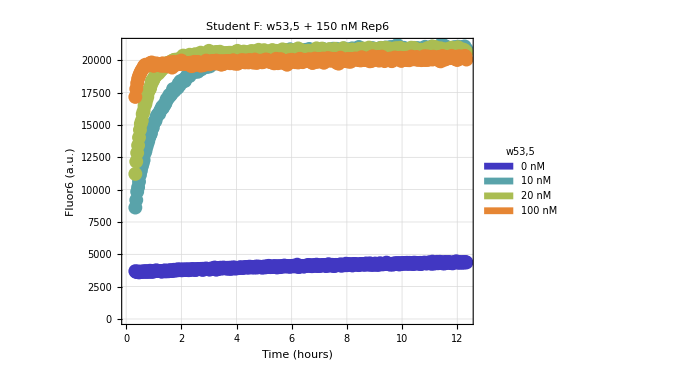

```mathematica
n=6;
trajectories={"0 nM", "10 nM", "20 nM", "100 nM"};
TrajectoryLabel="w53,5";
OutputLabel="Fluor6 (a.u.)"; 
CircuitLabel="Student F: w53,5 + 150 nM Rep6";  
PlotData[seesawWithout[[n,1]],trajectories,TrajectoryLabel,OutputLabel,CircuitLabel]
```

```mathematica
calibrationFormula[fluor_]:=0.0144477*fluor-0.425222
```

Rep23: 0.00504015*fluor-13.3691
Rep6: 0.0144477*fluor-0.425222
Equations from the solution set for Rep6 calibration data

```mathematica
concWithout1=Table[{seesawWithout[[t,1,s,d,1]],calibrationFormula[seesawWithout[[t,1,s,d,2]]]},{t,1,8},{s,1,4},{d,1,361}];
Dimensions[concWithout1]
```

{8,4,361,2}

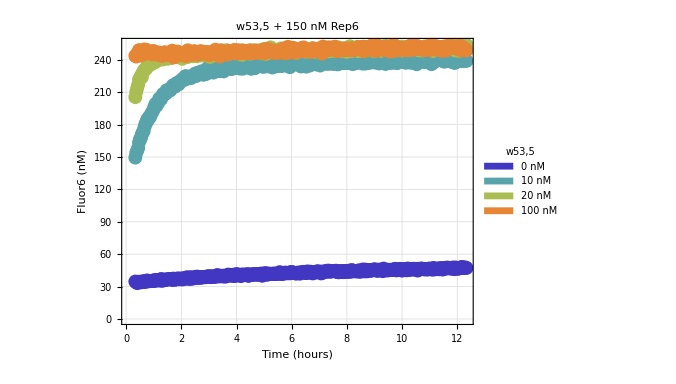
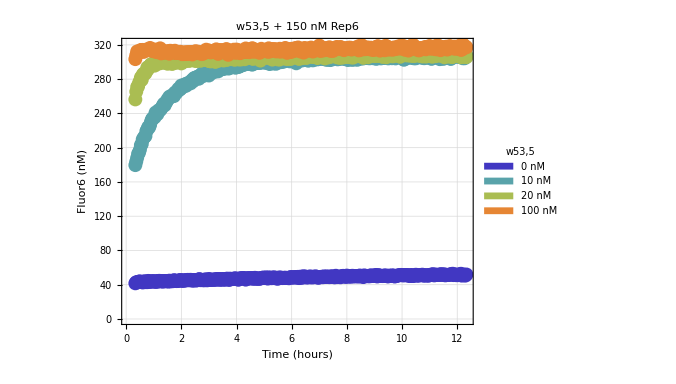
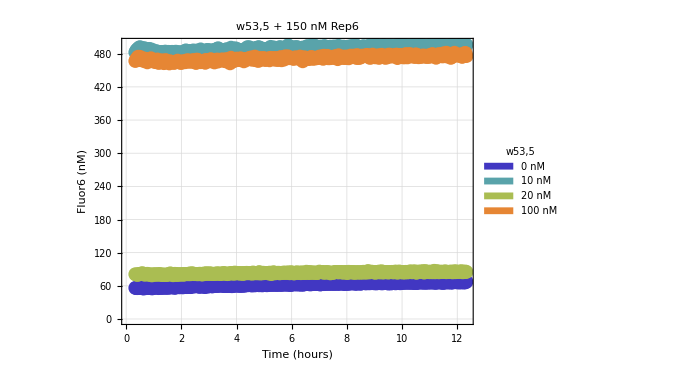
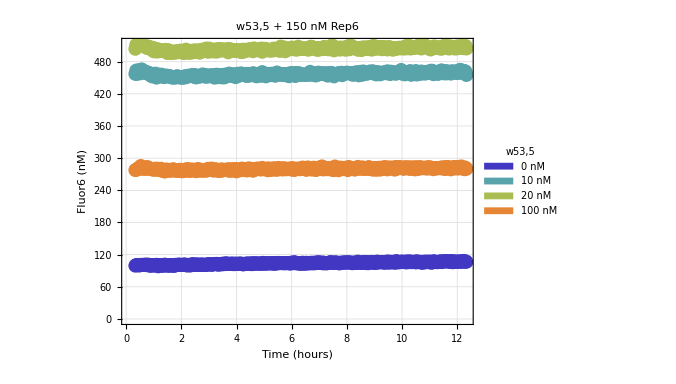
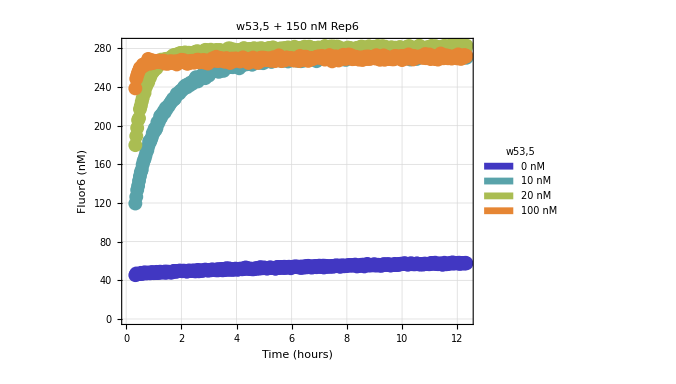
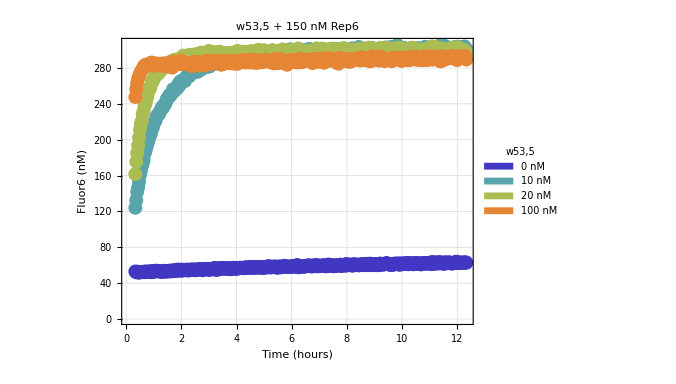
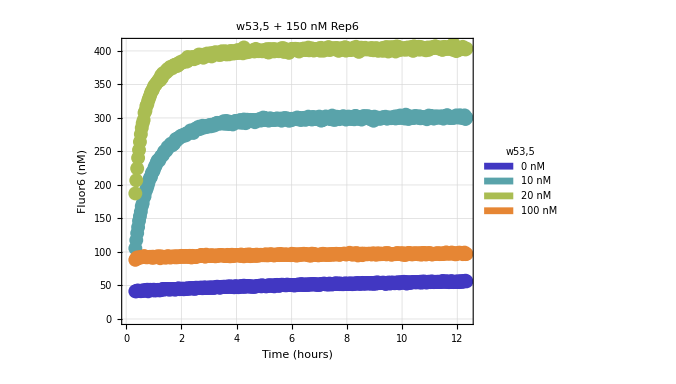
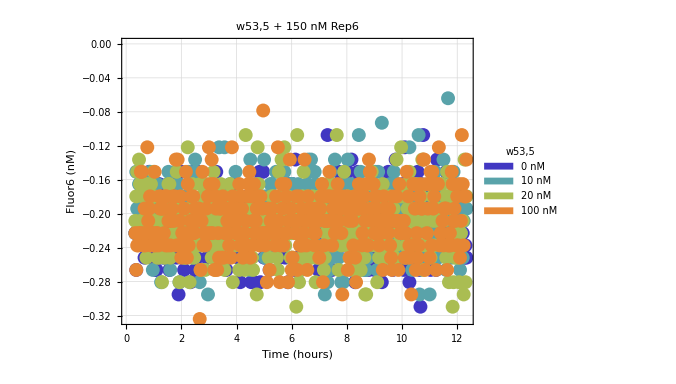

```mathematica
trajectories={"0 nM", "10 nM", "20 nM", "100 nM"};
TrajectoryLabel="w53,5";
OutputLabel="Fluor6 (nM)"; 
CircuitLabel="w53,5 + 150 nM Rep6";  
Table[PlotData[concWithout1[[s]],trajectories,TrajectoryLabel,OutputLabel,CircuitLabel],{s,1,8}]
```

```mathematica
referencelist={{1,0,0},{4,1,100}};
concWithout2=Table[NormalizeDataList[seesawWithout[[s,1]],referencelist],{s,1,8}];
```

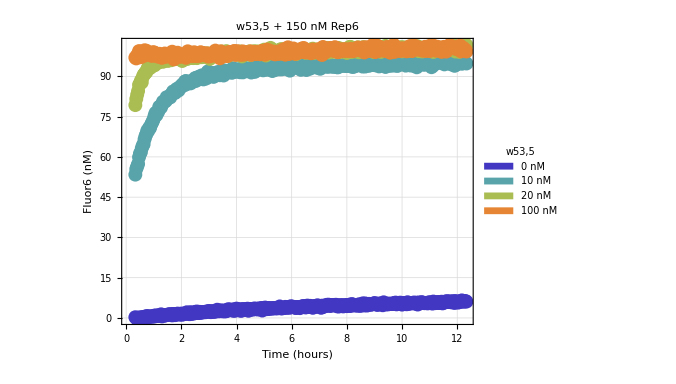
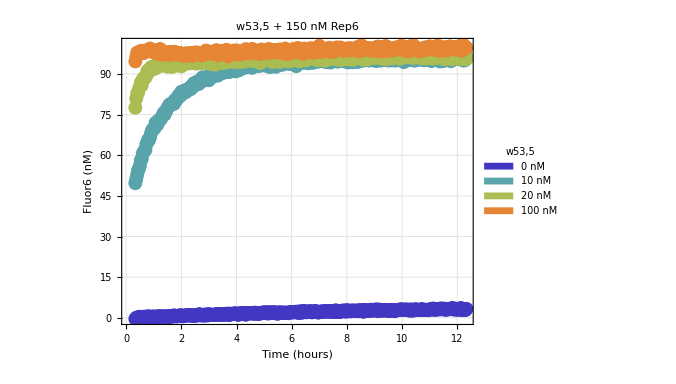
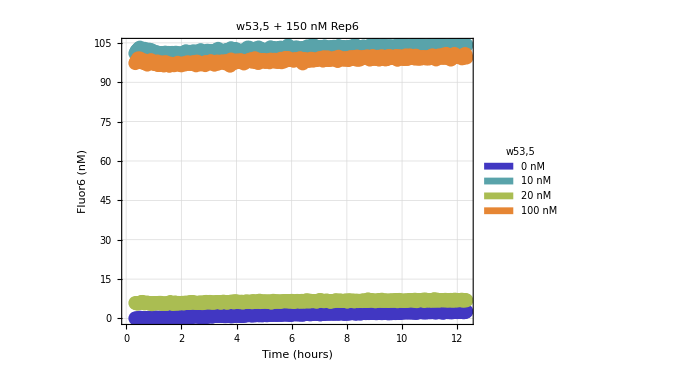
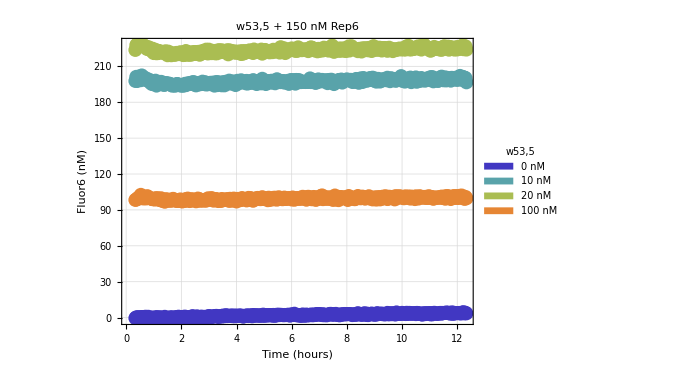
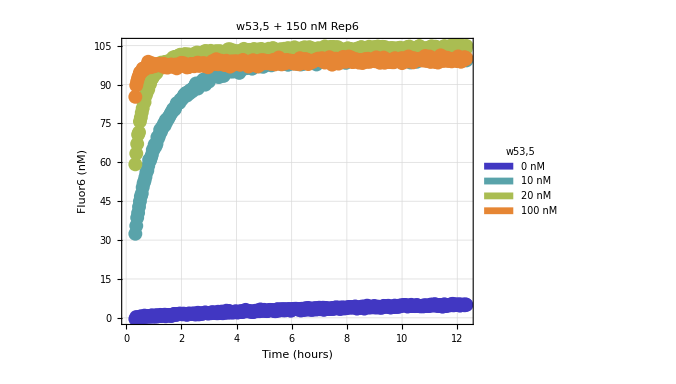
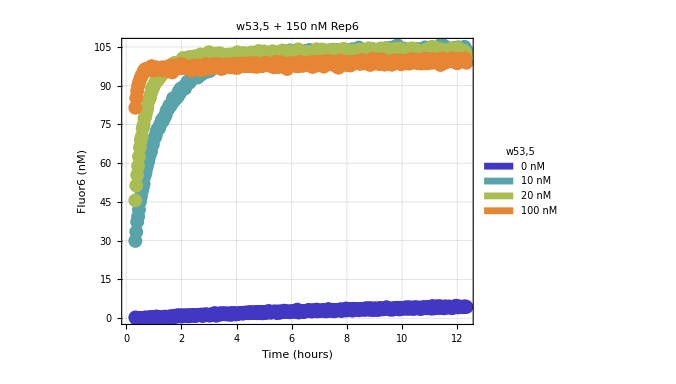
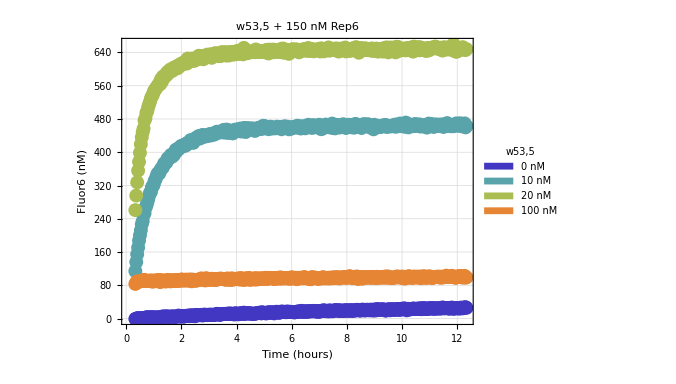
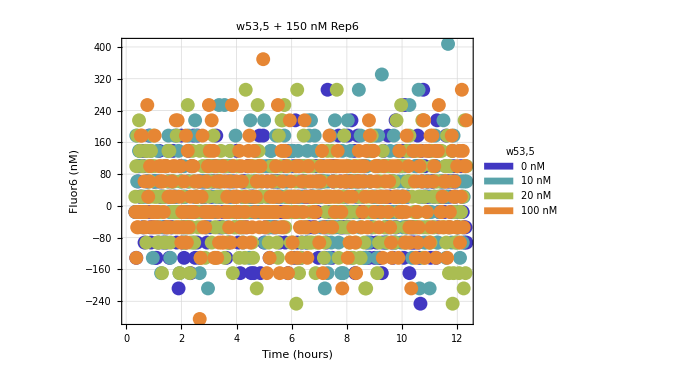

```mathematica
trajectories={"0 nM", "10 nM", "20 nM", "100 nM"};
TrajectoryLabel="w53,5";
OutputLabel="Fluor6 (nM)"; 
CircuitLabel="w53,5 + 150 nM Rep6";  
Table[PlotData[concWithout2[[s]],trajectories,TrajectoryLabel,OutputLabel,CircuitLabel],{s,1,8}]
```

The reference points method appears to be more useful here. The normalization from the calibration formula method found the concentrations of the trajectories to reach nearly 3 times the amount expected from the simulation. The excel data files seem to support this, as the raw fluorescence from the Lab 07 data appear to be higher than the raw fluorescence data for the Lab 06 data for similar input concentrations.

## Define input value and simulation time

```mathematica
OFF = 0.1;    
ON = 0.9;
input = {{0,0.1,0.2,1}};
time = 10; (* unit: hour *)
```

## Simulation

```mathematica
SIMcircuit=Table[
gatesys={
seesaw[5,{53},{7,6}],
reporter[6,5],
conc[g[5,w[5,6]],1*c],
conc[w[5,7],2*c],
conc[w[53,5],x1*c],
conc[W,(2+x1)*c],
conc[G,2.5*c],
conc[TH,1.1*0*c]
};
sol=gatesysToNDSolve[gatesys,time*60*60]//ReleaseHold//Flatten;
{Fluor[6][t*60*60]/c/.sol},
{x1,input[[1]]}
];
```

```mathematica
referencelistrelative={{1,0,0},{4,1,1}};
concWithoutRelative=Table[NormalizeDataList[seesawWithout[[s,1]],referencelistrelative],{s,1,8}];
```

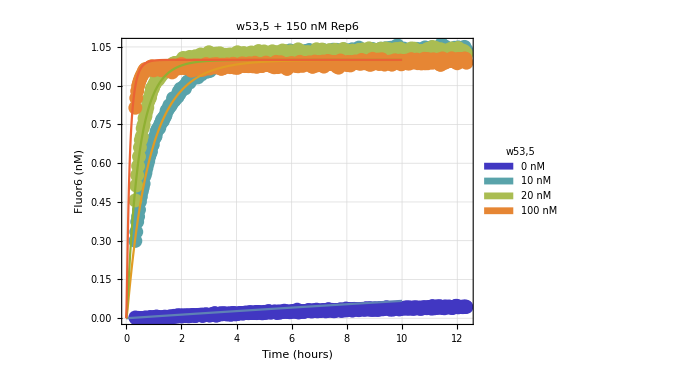

```mathematica
trajectories={"0 nM", "10 nM", "20 nM", "100 nM"};
TrajectoryLabel="w53,5";
OutputLabel="Fluor6 (nM)"; 
CircuitLabel="w53,5 + 150 nM Rep6";  
Show[{PlotData[concWithoutRelative[[6]],trajectories,TrajectoryLabel,OutputLabel,CircuitLabel],Plot[Evaluate[SIMcircuit//Flatten],{t,0,time},
Frame->True,FrameLabel->{"Time (hours)","Output"},
PlotStyle->{Thick},
PlotLegends->LineLegend[Automatic,{"Fluor[6]"}],
LabelStyle->Directive[FontSize->24,FontFamily->"Helvetica"],
PlotRange->All,AspectRatio->1/1.32,ImageSize->500]}]
```

They do agree pretty well for student F, but by adjusting the rate constant from 5 to 5.5, we can slightly improve it.

Other Plots

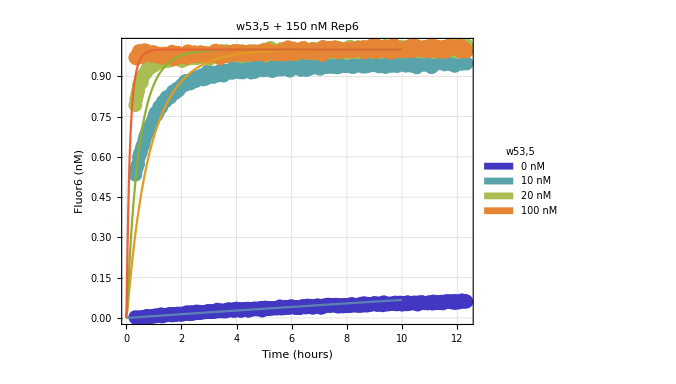
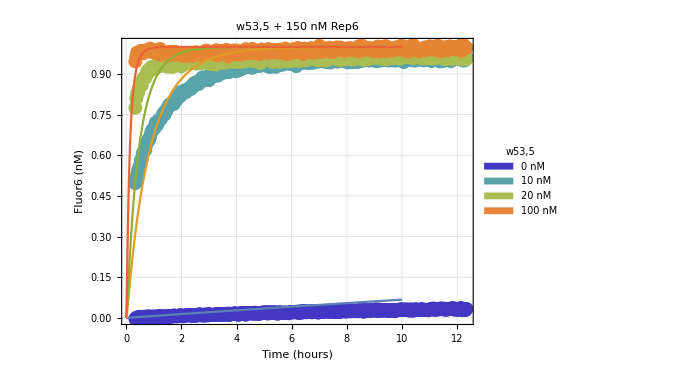
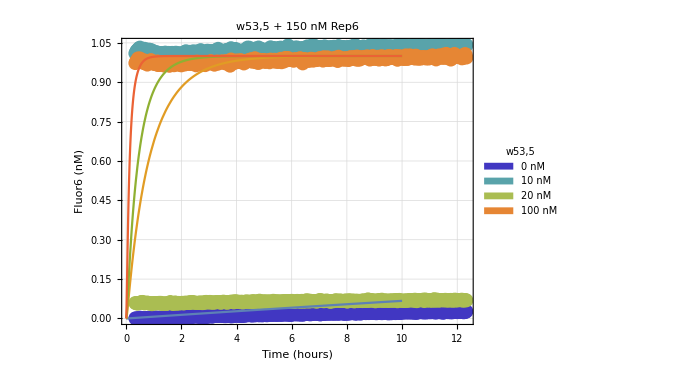
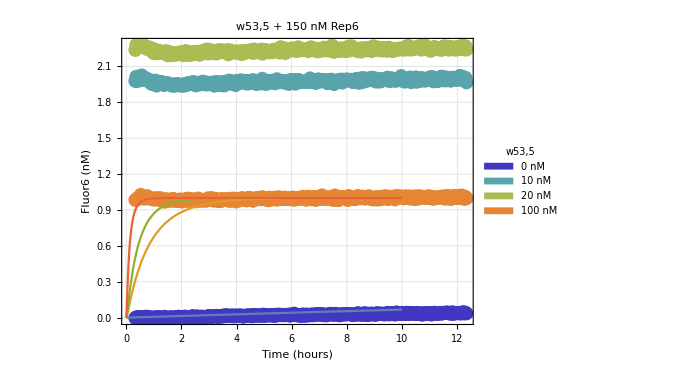
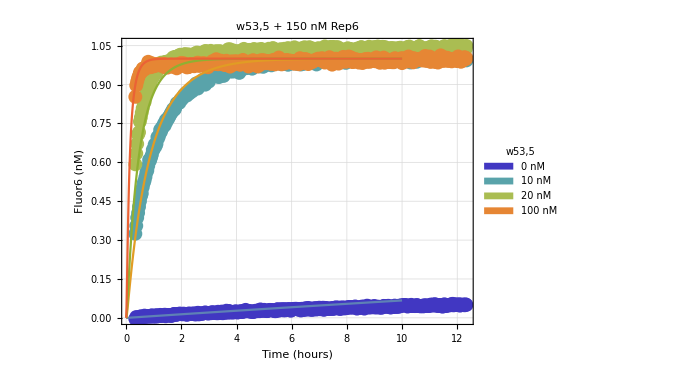
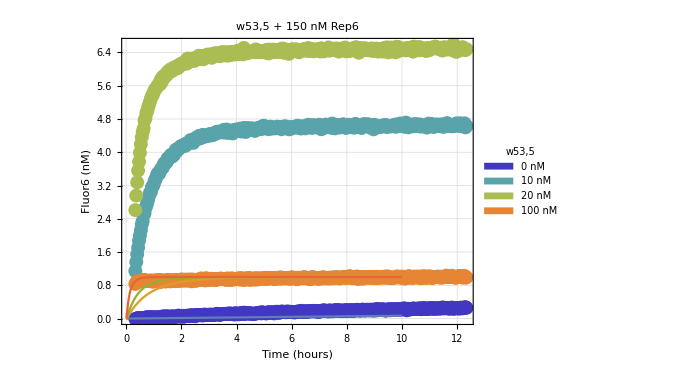
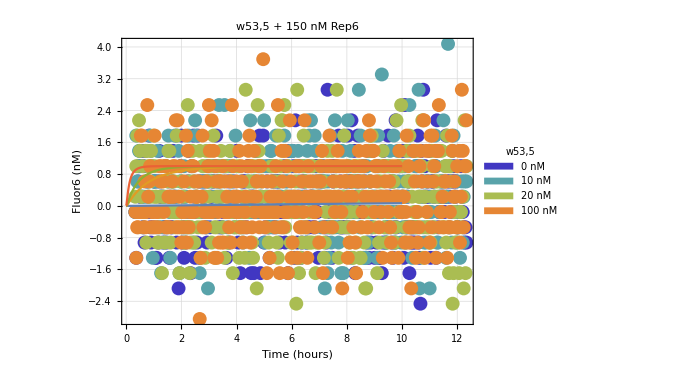
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[Show[{PlotData[concWithoutRelative[[s]],trajectories,TrajectoryLabel,OutputLabel,CircuitLabel],Plot[Evaluate[SIMcircuit//Flatten],{t,0,time},
Frame->True,FrameLabel->{"Time (hours)","Output"},
PlotStyle->{Thick},
PlotLegends->LineLegend[Automatic,{"Fluor[6]"}],
LabelStyle->Directive[FontSize->24,FontFamily->"Helvetica"],
PlotRange->All,AspectRatio->1/1.32,ImageSize->500]}],{s,1,8}]
```